```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/Tessa-Tom/RESULTS_29jan2017/Tall/TeAll_scripts_and_results/G_E0_Fel_Fqh_finiteSize/for_plotting/"];
file={"GibbsAll.Fqh_FinSizCor_Fel.out", "VFE.Fqh_FinSizCor_Fel.out"};
calphadFelFqh=Table[ReadList[file[[i]],{Number, Number,Number}],{i,1,file//Length}];
SetDirectory["/Volumes/MicroSD/Dropbox/Tessa-Tom/RESULTS_29jan2017/Tall/TeAll_scripts_and_results/G_E0_Fqh_finiteSize/for_plotting/"];
file={"GibbsAll.Fqh_FinSizCor_Fel.out", "VFE.Fqh_FinSizCor_Fel.out"};
calphadFqh=Table[ReadList[file[[i]],{Number, Number,Number}],{i,1,file//Length}];
```

```mathematica
fqhc=Transpose[{Transpose[calphadFelFqh[[2]]][[1]],Transpose[calphadFqh[[2]]][[2]]}];
fqhzr=Transpose[{Transpose[calphadFelFqh[[2]]][[1]],Transpose[calphadFqh[[2]]][[3]]}];
felfqhc=Transpose[{Transpose[calphadFelFqh[[2]]][[1]],Transpose[calphadFelFqh[[2]]][[2]]}];
felfqhzr=Transpose[{Transpose[calphadFelFqh[[2]]][[1]],Transpose[calphadFelFqh[[2]]][[3]]}];
```

```mathematica
options1={FrameLabel->{Style["T (K)",15],Style["Formation energy (eV/defect)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotStyle->Blue,PlotLegends->Placed[SwatchLegend[{Style["Carbon vacancy",15]}],{0.25,0.5}],PlotLabel->Style["Vacancy formation energy",15],PlotStyle->Thickness[0.007],PlotRange->{All,{-1.5,10}}};
options2={FrameLabel->{Style["T (K)",15],Style["Formation energy (eV/defect)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotStyle->Red,PlotLegends->Placed[SwatchLegend[{Style["Zirconium vacancy",15]}],{0.25,0.5}],PlotLabel->Style["Vacancy formation energy",15],PlotStyle->Thickness[0.007],PlotRange->{All,{-1.5,10}}};
```

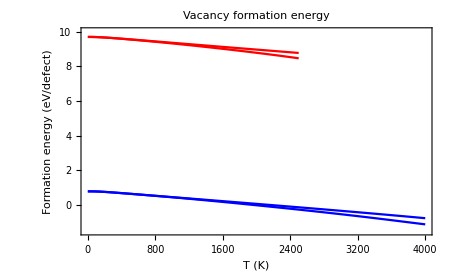

```mathematica
Show[{ListLinePlot[{fqhc,felfqhc},Evaluate[options1]],ListLinePlot[{fqhzr[[1;;2500]],felfqhzr[[1;;2500]]},Evaluate[options2]]}]
```

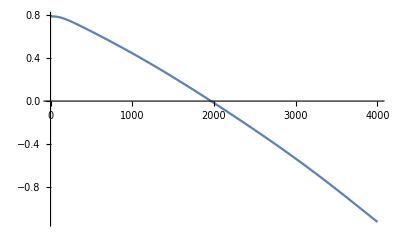

-Graphics-

```mathematica
ListLinePlot@fqhc
ListLinePlot@felfqhc
```